## Markov chain associated to the single-bit flip mutation operator on a two-dimensional binary Hamming graph

```mathematica
hyp22=HypercubeGraph[2];
hyp22Adj=AdjacencyMatrix[hyp22];
hyp22Diag=DiagonalMatrix[VertexDegree[hyp22]];
(* Transition matrix: T = AD^-1 *)
hyp22Trans=hyp22Adj.Inverse[hyp22Diag];
```

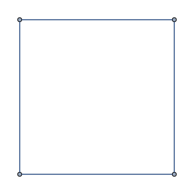

```mathematica
hyp22
```

```mathematica
hyp22Trans//MatrixForm
```

(0 | 1/2 | 1/2 | 0
1/2 | 0 | 0 | 1/2
1/2 | 0 | 0 | 1/2
0 | 1/2 | 1/2 | 0)

```mathematica
start1={1,0,0,0}; (* initial probability distribution over states *)
p1=DiscreteMarkovProcess[start1,hyp22Trans];
```

```mathematica
Graph[p1,VertexSize->0.3,VertexStyle->LightGray,VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[FontFamily->"Latin Modern Math",FontSize->35],PerformanceGoal->"Quality",EdgeStyle->Directive[Black],EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.1]]
```

-Graphics-

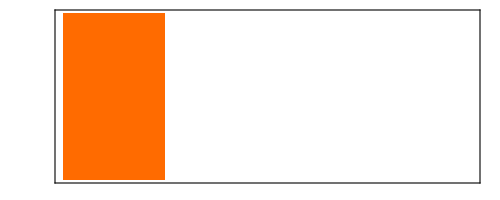
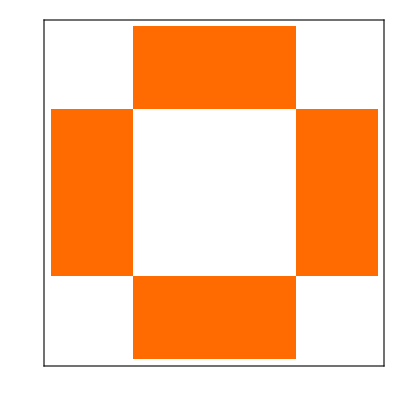
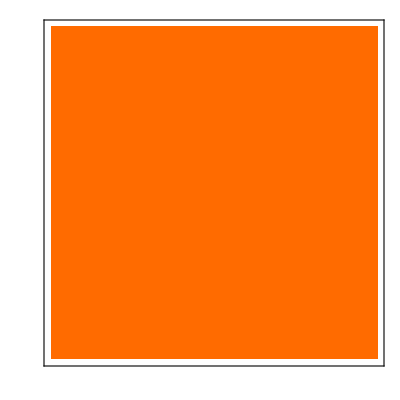
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0,0,0,0}
HoldingTimeVariance | {0,0,0,0}
Structural Properties | 
CommunicatingClasses | {1,2,3,4}
RecurrentClasses | {1,2,3,4}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | {1,2,3,4}
Periods | {2}
Irreducible | True
Primitive | False
Aperiodic | False
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | True

```mathematica
MarkovProcessProperties[p1]
```

```mathematica
(* Stationary probability distribution over all four states *)
(PDF[StationaryDistribution[p1],#] &) /@ Range[4]
```

{1/4,1/4,1/4,1/4}

## Markov chain associated to the single-bit flip mutation operator on a three-dimensional binary Hamming graph

```mathematica
hyp32=HypercubeGraph[3];
hyp32Adj=AdjacencyMatrix[hyp32];
hyp32Diag=DiagonalMatrix[VertexDegree[hyp32]];
hyp32Trans=hyp32Adj.Inverse[hyp32Diag];
```

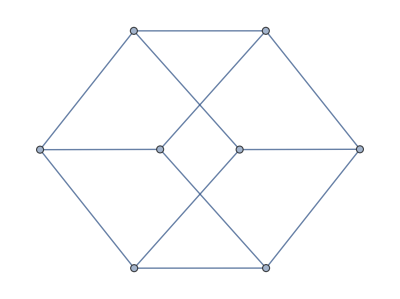

```mathematica
hyp32
```

```mathematica
hyp32Trans//MatrixForm
```

(0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0
1/3 | 0 | 0 | 1/3 | 0 | 1/3 | 0 | 0
1/3 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | 0
0 | 1/3 | 1/3 | 0 | 0 | 0 | 0 | 1/3
1/3 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 0
0 | 1/3 | 0 | 0 | 1/3 | 0 | 0 | 1/3
0 | 0 | 1/3 | 0 | 1/3 | 0 | 0 | 1/3
0 | 0 | 0 | 1/3 | 0 | 1/3 | 1/3 | 0)

```mathematica
start2={1,0,0,0,0,0,0,0};
p2=DiscreteMarkovProcess[start2,hyp32Trans];
```

```mathematica
Graph[p2,VertexSize->0.5,VertexStyle->LightGray,VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[FontFamily->"Latin Modern Math",FontSize->30],PerformanceGoal->"Quality",EdgeStyle->Black]
```

-Graphics-

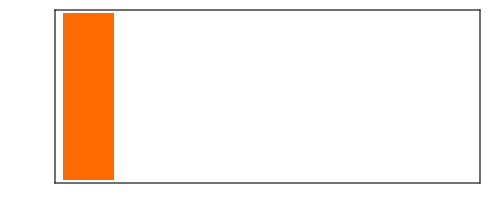
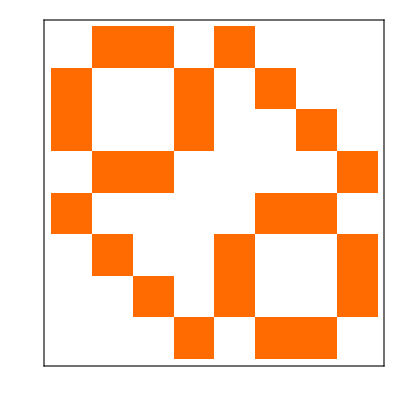
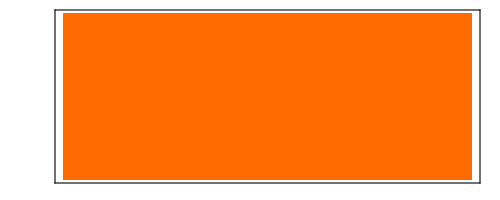
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | -Graphics-
HoldingTimeVariance | -Graphics-
Structural Properties | 
CommunicatingClasses | {1,…,8}
RecurrentClasses | {1,…,8}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | {1,…,8}
Periods | {2}
Irreducible | True
Aperiodic | False
Primitive | False
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | True

```mathematica
MarkovProcessProperties[p2]
```

```mathematica
(PDF[StationaryDistribution[p2],#] &) /@ Range[8]
```

{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8}

## Markov chain associated to the uniform crossover operator on a three-dimensional binary Hamming graph

### Uniform crossover operator for Boolean spaces with Hamming distance

Each binary crossover operator can be defined in terms of a binary 'mask', indicating for each bit position of the 'offspring' whether the value at that position is taken from the 'father' or the 'mother'. The uniform crossover operator is defined by all possible masks applied to the parents.

```mathematica
masks[dim_]:=Tuples[{0,1},dim];
crossoverMasked[father_,mother_,mask_,dim_]:=
Table[If[mask[[i]]==0,
			father[[i]],
			mother[[i]]],
	 {i,dim}];
unifCrossover[father_,mother_,dim_]:= DeleteDuplicates[((crossoverMasked[father,mother,#,dim])&)/@masks[dim]];
```

### Generalised adjacency matrix and transition matrix for the uniform crossover

See (Stadler and Wagner, 1998, Algebraic Theory of Recombination Spaces) for the formal definitions.

```mathematica
unifCrossoverSmatrix[dim_]:= Table[2*((3/2)^dim)*(3^(-HammingDistance[x,y])),{x,masks[dim]},{y,masks[dim]}];
```

```mathematica
(* Transition matrix T = 1/(2|X|) S. For the three-dimensional binary Hamming graph |X| = 2^3= 8 *)
unifCrossoverTrans[dim_]:=(1/(2*(2^dim)))unifCrossoverSmatrix[dim];
```

```mathematica
unifCrossoverSmatrix[3]//MatrixForm
```

(27/4 | 9/4 | 9/4 | 3/4 | 9/4 | 3/4 | 3/4 | 1/4
9/4 | 27/4 | 3/4 | 9/4 | 3/4 | 9/4 | 1/4 | 3/4
9/4 | 3/4 | 27/4 | 9/4 | 3/4 | 1/4 | 9/4 | 3/4
3/4 | 9/4 | 9/4 | 27/4 | 1/4 | 3/4 | 3/4 | 9/4
9/4 | 3/4 | 3/4 | 1/4 | 27/4 | 9/4 | 9/4 | 3/4
3/4 | 9/4 | 1/4 | 3/4 | 9/4 | 27/4 | 3/4 | 9/4
3/4 | 1/4 | 9/4 | 3/4 | 9/4 | 3/4 | 27/4 | 9/4
1/4 | 3/4 | 3/4 | 9/4 | 3/4 | 9/4 | 9/4 | 27/4)

```mathematica
unifCrossoverTrans[3]//MatrixForm
```

(27/64 | 9/64 | 9/64 | 3/64 | 9/64 | 3/64 | 3/64 | 1/64
9/64 | 27/64 | 3/64 | 9/64 | 3/64 | 9/64 | 1/64 | 3/64
9/64 | 3/64 | 27/64 | 9/64 | 3/64 | 1/64 | 9/64 | 3/64
3/64 | 9/64 | 9/64 | 27/64 | 1/64 | 3/64 | 3/64 | 9/64
9/64 | 3/64 | 3/64 | 1/64 | 27/64 | 9/64 | 9/64 | 3/64
3/64 | 9/64 | 1/64 | 3/64 | 9/64 | 27/64 | 3/64 | 9/64
3/64 | 1/64 | 9/64 | 3/64 | 9/64 | 3/64 | 27/64 | 9/64
1/64 | 3/64 | 3/64 | 9/64 | 3/64 | 9/64 | 9/64 | 27/64)

Verify that indeed each row of the transition matrix adds up to 1:

```mathematica
Total[((unifCrossoverTrans[3][[#]]&)/@ Range[8])]
```

{1,1,1,1,1,1,1,1}

```mathematica
start3={1,0,0,0,0,0,0,0};
p3=DiscreteMarkovProcess[start3,unifCrossoverTrans[3]];
```

```mathematica
Graph[p3,VertexSize->0.28,VertexStyle->LightGray,VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[FontFamily->"Latin Modern Math",FontSize->20],PerformanceGoal->"Quality",EdgeStyle->Black]
```

-Graphics-

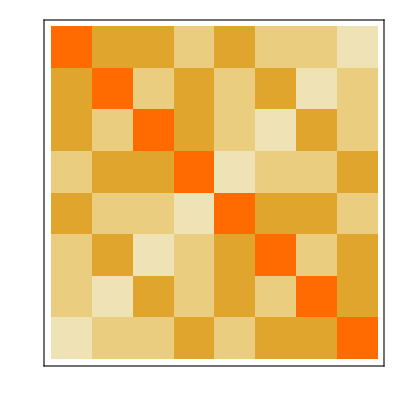
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | -Graphics-
HoldingTimeVariance | -Graphics-
Structural Properties | 
CommunicatingClasses | {1,…,8}
RecurrentClasses | {1,…,8}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | None
Periods | {}
Irreducible | True
Aperiodic | True
Primitive | True
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | True

```mathematica
MarkovProcessProperties[p3]
```

```mathematica
(PDF[StationaryDistribution[p3],#] &) /@ Range[8]
```

{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8}